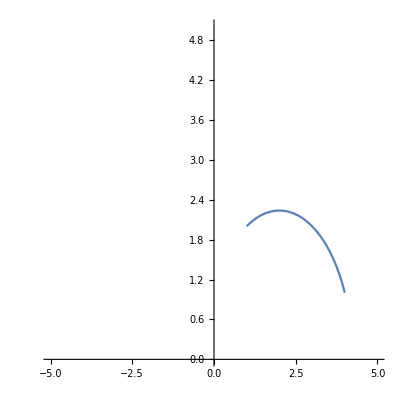

```mathematica
PoincareGeodesic[P1_,P2_]:=Module[{x1,y1,x2,y2,z,r,center,theta1,theta2},{x1,y1}=P1;
{x2,y2}=P2;
(*Caso trivial:línea vertical*)If[x1==x2,Return[ParametricPlot[{x1,t},{t,Min[y1,y2],Max[y1,y2]},PlotRange->{{-5,5},{0,5}},Axes->True,AxesOrigin->{0,0},AspectRatio->1]]];
(*Centro y radio de la circunferencia*)z=(x1^2+y1^2-x2^2-y2^2)/(2 (x1-x2));
r=Sqrt[(x1-z)^2+y1^2];
center={z,0};
(*Ángulos para el arco de circunferencia*)theta1=ArcTan[x1-z,y1];
theta2=ArcTan[x2-z,y2];
(*Dibujar el arco completo*)ParametricPlot[center+r {Cos[t],Sin[t]},{t,Min[theta1,theta2],Max[theta1,theta2]},PlotRange->{{-5,5},{0,5}},Axes->True,AxesOrigin->{0,0},AspectRatio->1]]

(*Ejemplo:Graficar la geodésica de Poincaré entre dos puntos P1 y P2*)
P1={1,2};
P2={4,1};
PoincareGeodesic[P1,P2]
```

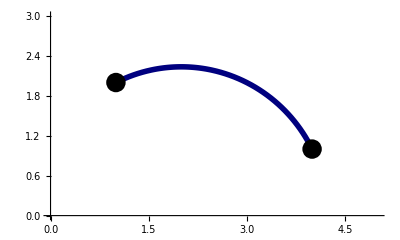

```mathematica
PoincareGeodesic[P1_,P2_]:=Module[{x1,y1,x2,y2,z,r,center,theta1,theta2,curve,points},{x1,y1}=P1;
{x2,y2}=P2;
(*Puntos grandes*)points=Graphics[{Black,AbsolutePointSize[14],Point[P1],Point[P2]}];
(*Caso trivial:línea vertical*)If[x1==x2,Show[points,ParametricPlot[{x1,t},{t,Min[y1,y2],Max[y1,y2]},PlotStyle->Thick,PlotRange->{{-5,5},{0,5}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic]],(*Caso general:Arco de circunferencia*)z=(x1^2+y1^2-x2^2-y2^2)/(2 (x1-x2));
r=Sqrt[(x1-z)^2+y1^2];
center={z,0};
(*Ángulos para el arco de circunferencia*)theta1=ArcTan[x1-z,y1];
theta2=ArcTan[x2-z,y2];
curve=ParametricPlot[center+r {Cos[t],Sin[t]},{t,Min[theta1,theta2],Max[theta1,theta2]},PlotStyle->{RGBColor[0, 0, 0.498039],Thickness[0.01]},PlotRange->{{0,5},{0,3}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic];
Show[curve,points]]]

(*Ejemplo:Graficar la geodésica de Poincaré entre dos puntos P1 y P2*)
P1={1,2};
P2={4,1};
PoincareGeodesic[P1,P2]
```

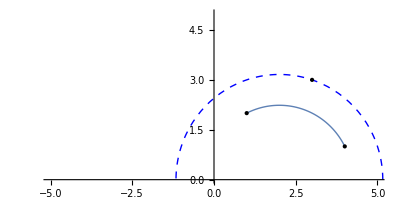

```mathematica
(*PoincareGeodesic:Dibuja la geodésica entre P1 y P2 y una curva paralela pasando por P3*)PoincareGeodesicParallel[P1_,P2_,P3_]:=Module[{x1,y1,x2,y2,x3,y3,z,r,center,theta1,theta2,r3,curve,parallelCurve,points},{x1,y1}=P1;
{x2,y2}=P2;
{x3,y3}=P3;
(*Graficar puntos*)points=Graphics[{Black,PointSize[Large],Point[P1],Point[P2],Point[P3]}];
If[x1==x2,(*Caso especial:Línea vertical*)curve=ParametricPlot[{x1,t},{t,Min[y1,y2],Max[y1,y2]},PlotStyle->Thick,PlotRange->{{-5,5},{0,5}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->400];
parallelCurve=ParametricPlot[{x3,t},{t,0,y3},PlotStyle->{Thick,Dashed,Blue},PlotRange->{{-5,5},{0,5}},Axes->None,AspectRatio->Automatic,ImageSize->400];
Return[Show[curve,parallelCurve,points]];];
(*Centro y radio de la circunferencia*)z=(x1^2+y1^2-x2^2-y2^2)/(2 (x1-x2));
r=Sqrt[(x1-z)^2+y1^2];
center={z,0};
(*Ángulos para la geodésica original*)theta1=ArcTan[x1-z,y1];
theta2=ArcTan[x2-z,y2];
(*Radio de la circunferencia que pasa por P3 y es paralela a la original*)r3=Sqrt[(x3-z)^2+y3^2];
(*Geodésica original*)curve=ParametricPlot[center+r {Cos[t],Sin[t]},{t,Min[theta1,theta2],Max[theta1,theta2]},PlotStyle->Thick,PlotRange->{{-5,5},{0,5}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->400];
(*Curva paralela que pasa por P3*)parallelCurve=ParametricPlot[center+r3 {Cos[t],Sin[t]},{t,0,Pi},PlotStyle->{Thick,Dashed,Blue},PlotRange->{{-5,5},{0,5}},Axes->None,AspectRatio->Automatic,ImageSize->400];
Show[curve,parallelCurve,points]]

(*Ejemplo:Graficar la geodésica entre P1 y P2 y su curva paralela que pasa por P3*)
P1={1,2};
P2={4,1};
P3={3,3};
PoincareGeodesicParallel[P1,P2,P3]
```

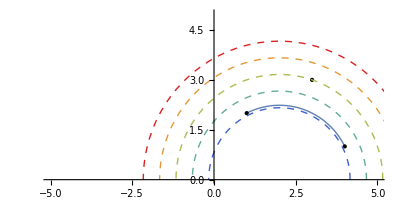

```mathematica
(*PoincareGeodesic:Dibuja la geodésica entre P1 y P2 y cinco curvas paralelas*)PoincareGeodesicParallels[P1_,P2_,P3_]:=Module[{x1,y1,x2,y2,x3,y3,z,r,center,theta1,theta2,r3,curve,parallelCurves,points,radii,colors},{x1,y1}=P1;
{x2,y2}=P2;
{x3,y3}=P3;
(*Graficar puntos*)points=Graphics[{Black,PointSize[Large],Point[P1],Point[P2],Point[P3]}];
If[x1==x2,(*Caso especial:Línea vertical*)curve=ParametricPlot[{x1,t},{t,Min[y1,y2],Max[y1,y2]},PlotStyle->Thick,PlotRange->{{-5,5},{0,5}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->400];
parallelCurves=Table[ParametricPlot[{x3+0.5 (k-3),t},{t,0,y3},PlotStyle->{Thick,Dashed,ColorData["Rainbow"][k/5]},PlotRange->{{-5,5},{0,5}},Axes->None,AspectRatio->Automatic,ImageSize->400],{k,1,5}];
Return[Show[curve,points,parallelCurves]];];
(*Centro y radio de la circunferencia original*)z=(x1^2+y1^2-x2^2-y2^2)/(2 (x1-x2));
r=Sqrt[(x1-z)^2+y1^2];
center={z,0};
(*Ángulos para la geodésica original*)theta1=ArcTan[x1-z,y1];
theta2=ArcTan[x2-z,y2];
(*Radio de la circunferencia que pasa por P3 y es paralela a la original*)r3=Sqrt[(x3-z)^2+y3^2];
(*Crear un conjunto de radios para las curvas paralelas*)radii=Table[r3+(k-3)*0.5,{k,1,5}];
(*Colores para distinguir cada curva paralela*)colors=Table[ColorData["Rainbow"][k/5],{k,1,5}];
(*Geodésica original*)curve=ParametricPlot[center+r {Cos[t],Sin[t]},{t,Min[theta1,theta2],Max[theta1,theta2]},PlotStyle->Thick,PlotRange->{{-5,5},{0,5}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->400];
(*Curvas paralelas*)parallelCurves=Table[ParametricPlot[center+radii[[k]] {Cos[t],Sin[t]},{t,0,Pi},PlotStyle->{Thick,Dashed,colors[[k]]},PlotRange->{{-5,5},{0,5}},Axes->None,AspectRatio->Automatic,ImageSize->400],{k,1,5}];
Show[curve,points,parallelCurves]]

(*Ejemplo:Graficar la geodésica entre P1 y P2 y cinco curvas paralelas que pasan cerca de P3*)
P1={1,2};
P2={4,1};
P3={3,3};
PoincareGeodesicParallels[P1,P2,P3]
```

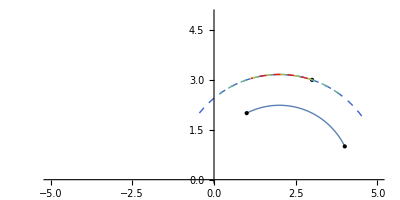

```mathematica
(*PoincareGeodesicParallels:Dibuja la geodésica entre P1 y P2 y cinco curvas paralelas que pasan por P3*)PoincareGeodesicParallels[P1_,P2_,P3_]:=Module[{x1,y1,x2,y2,x3,y3,z,r,center,theta1,theta2,r3,curve,parallelCurves,points,angles,colors},{x1,y1}=P1;
{x2,y2}=P2;
{x3,y3}=P3;
(*Graficar puntos*)points=Graphics[{Black,PointSize[Large],Point[P1],Point[P2],Point[P3]}];
If[x1==x2,(*Caso especial:Línea vertical*)curve=ParametricPlot[{x1,t},{t,Min[y1,y2],Max[y1,y2]},PlotStyle->Thick,PlotRange->{{-5,5},{0,5}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->400];
Return[Show[curve,points]];];
(*Centro y radio de la circunferencia original*)z=(x1^2+y1^2-x2^2-y2^2)/(2 (x1-x2));
r=Sqrt[(x1-z)^2+y1^2];
center={z,0};
(*Ángulos para la geodésica original*)theta1=ArcTan[x1-z,y1];
theta2=ArcTan[x2-z,y2];
(*Radio de la circunferencia que pasa por P3 y es paralela a la original*)r3=Sqrt[(x3-z)^2+y3^2];
(*Geodésica principal entre P1 y P2*)curve=ParametricPlot[center+r {Cos[t],Sin[t]},{t,Min[theta1,theta2],Max[theta1,theta2]},PlotStyle->Thick,PlotRange->{{-5,5},{0,5}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->400];
(*Crear ángulos desplazados para curvas paralelas que pasan por P3*)angles=Table[ArcTan[x3-z,y3]+(k-3)*0.3,{k,1,5}];
colors=Table[ColorData["Rainbow"][k/5],{k,1,5}];
(*Curvas paralelas que pasan por P3*)parallelCurves=Table[ParametricPlot[center+r3 {Cos[t],Sin[t]},{t,Min[angles[[k]],Pi-angles[[k]]],Max[angles[[k]],Pi-angles[[k]]]},PlotStyle->{Thick,Dashed,colors[[k]]},PlotRange->{{-5,5},{0,5}},Axes->None,AspectRatio->Automatic,ImageSize->400],{k,1,5}];
Show[curve,points,parallelCurves]]

(*Ejemplo:Graficar la geodésica entre P1 y P2 y cinco curvas paralelas que pasan por P3*)
P1={1,2};
P2={4,1};
P3={3,3};
PoincareGeodesicParallels[P1,P2,P3]
```

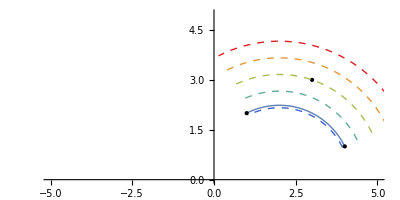

```mathematica
(*PoincareGeodesic:Dibuja la geodésica entre P1 y P2 y cinco curvas paralelas que pasan por P3*)PoincareGeodesicParallels[P1_,P2_,P3_]:=Module[{x1,y1,x2,y2,x3,y3,z,r,center,theta1,theta2,r3,curve,parallelCurves,points,radii,colors},{x1,y1}=P1;
{x2,y2}=P2;
{x3,y3}=P3;
(*Graficar puntos*)points=Graphics[{Black,PointSize[Large],Point[P1],Point[P2],Point[P3]}];
If[x1==x2,(*Caso especial:Línea vertical*)curve=ParametricPlot[{x1,t},{t,Min[y1,y2],Max[y1,y2]},PlotStyle->Thick,PlotRange->{{-5,5},{0,5}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->400];
parallelCurves=Table[ParametricPlot[{x3,t},{t,0,y3+(k-3)*0.5},PlotStyle->{Thick,Dashed,ColorData["Rainbow"][k/5]},PlotRange->{{-5,5},{0,5}},Axes->None,AspectRatio->Automatic,ImageSize->400],{k,1,5}];
Return[Show[curve,points,parallelCurves]];];
(*Centro y radio de la circunferencia original*)z=(x1^2+y1^2-x2^2-y2^2)/(2 (x1-x2));
r=Sqrt[(x1-z)^2+y1^2];
center={z,0};
(*Ángulos para la geodésica original*)theta1=ArcTan[x1-z,y1];
theta2=ArcTan[x2-z,y2];
(*Radio de la circunferencia que pasa por P3*)r3=Sqrt[(x3-z)^2+y3^2];
(*Crear cinco radios diferentes alrededor de P3*)radii=Table[r3+(k-3)*0.5,{k,1,5}];
colors=Table[ColorData["Rainbow"][k/5],{k,1,5}];
(*Geodésica original*)curve=ParametricPlot[center+r {Cos[t],Sin[t]},{t,Min[theta1,theta2],Max[theta1,theta2]},PlotStyle->Thick,PlotRange->{{-5,5},{0,5}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->400];
(*Curvas paralelas que pasan por P3*)parallelCurves=Table[Module[{rParallel,theta3,thetaMin,thetaMax},rParallel=radii[[k]];
theta3=ArcTan[x3-z,y3];
thetaMin=theta3-Pi/4;
thetaMax=theta3+Pi/4;
ParametricPlot[center+rParallel {Cos[t],Sin[t]},{t,thetaMin,thetaMax},PlotStyle->{Thick,Dashed,colors[[k]]},PlotRange->{{-5,5},{0,5}},Axes->None,AspectRatio->Automatic,ImageSize->400]],{k,1,5}];
Show[curve,points,parallelCurves]]

(*Ejemplo:Graficar la geodésica entre P1 y P2 y cinco curvas paralelas que pasan por P3*)
P1={1,2};
P2={4,1};
P3={3,3};
PoincareGeodesicParallels[P1,P2,P3]
```